```mathematica
σ={10.96,10.96}(*Femto Meter^2*);
β={0.8775^2,0.8775^2}(*Femto Meter^2*);
ep={-0.4722013538300519,-0.4722013538300519};
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
(*k=1.85(*Femto Meter^-1*);*)
m=938.272046(*Mega ElectronVolt*);
```

```mathematica
F=σ/(4*Pi*β)*(1-I*ep);
η=1/(2*β);
```

```mathematica
g={F[[1]],F[[1]],F[[2]],-F[[1]]*F[[1]],-F[[1]]*F[[2]],-F[[1]]*F[[2]],F[[1]]*F[[1]]*F[[2]]};
tempa={η[[1]],η[[1]],η[[2]],2*η[[1]],η[[1]]+η[[2]],η[[1]]+η[[2]],2*η[[1]]+η[[2]]};
tempb={4/9*η[[1]],4/9*η[[1]],η[[2]]/9,8/9*η[[1]],4/9η[[1]]+η[[2]]/9,4/9*η[[1]]+η[[2]]/9,8/9*η[[1]]+η[[2]]/9};
tempc={η[[1]]/4,η[[1]]/4,0,η[[1]]/2,η[[1]]/4,η[[1]]/4,η[[1]]/2};
tempd={4/3*η[[1]],4/3*η[[1]],-2/3*η[[2]],8/3*η[[1]],4/3*η[[1]]-2/3*η[[2]],4/3*η[[1]]-2/3*η[[2]],8/3*η[[1]]-2/3*η[[2]]};
tempe={η[[1]],-η[[1]],0,0,η[[1]],-η[[1]],0};
temph={-2/3*η[[1]],2/3*η[[1]],0,0,-2/3*η[[1]],2/3*η[[1]],0};
```

```mathematica
β0={0.025525,0.080309,0.14877,0.25267,0.46807,1.4727};
α0={0.0014379,0.013487,0.040847,0.092103,0.18785,0.38315,0.86392,2.6165,24.542};
C0={{9.6395*10^-6,6.5959*10^-4,-2.2601*10^-3,2.5861*10^-3,-1.1006*10^-3,1.7251*10^-4},{-3.8282*10^-3,1.8785*10^-2,1.5663*10^-2,-3.8442*10^-2,1.6119*10^-2,-1.2993*10^-3},{-1.0250*10^-2,-7.0482*10^-2,7.1581*10^-2,1.8595*10^-1,-8.3598*10^-2,2.5213*10^-4},{5.3943*10^-3,4.7633*10^-2,-5.3326*10^-1,5.0441*10^-1,1.5834*10^-1,1.3848*10^-2},{-1.3885*10^-2,-1.0979*10^-1,7.5942*10^-1,-1.4875,6.4663*10^-1,-3.0116*10^-2},{7.9833*10^-4,5.6057*10^-2,-6.1065*10^-1,1.0816,-5.6129*10^-1,5.1744*10^-2},{-8.8342*10^-3,-5.9414*10^-2,2.5320*10^-1,-5.2121*10^-1,3.6938*10^-1,3.9780*10^-2},{3.3161*10^-2,1.2733*10^-1,4.3251*10^-2,3.0788*10^-1,-6.0045*10^-1,-7.5965*10^-2},{-2.5412*10^-3,-1.1125*10^-2,6.5278*10^-3,-4.1054*10^-2,5.9130*10^-2,7.9525*10^-4}};
```

```mathematica
β1={3.8566*10^-2,1.2955*10^-1,2.9017*10^-1,9.7471*10^-1};
α1={4.7124*10^-3,4.8770*10^-2,1.8785*10^-1,7.2358*10^-1,7.4885};
C1={{6.1464*10^-6,4.6065*10^-6,-2.2756*10^-5,4.7736*10^-6},{3.6418*10^-5,2.2433*10^-3,3.4320*10^-3,-6.8707*10^-4},{1.9483*10^-5,-2.9031*10^-3,2.0603*10^-2,1.2715*10^-2},{-3.0275*10^-5,1.4127*10^-3,-2.3423*10^-2,-2.8375*10^-3},{-1.2199*10^-5,-1.6321*10^-3,-2.9310*10^-3,4.6651*10^-3}};
```

```mathematica
a=Array[tempa[[#5]]&,{5,5,4,4,7}];
b=Array[tempb[[#5]]&,{5,5,4,4,7}];
c=Array[tempc[[#5]]&,{5,5,4,4,7}];
d=Array[tempd[[#5]]&,{5,5,4,4,7}];
e=Array[tempe[[#5]]&,{5,5,4,4,7}];
h=Array[temph[[#5]]&,{5,5,4,4,7}];
```

```mathematica
αii1=Array[α1[[#1]]+α1[[#2]]&,{5,5,4,4,7}];
βjj1=Array[β1[[#3]]+β1[[#4]]&,{5,5,4,4,7}];
bkj1=Array[b[[#5]]+βjj1[[#1]][[#2]][[#3]][[#4]][[#5]]&,{5,5,4,4,7}];
cki1=Array[c[[#5]]+αii1[[#1]][[#2]][[#3]][[#4]][[#5]]&,{5,5,4,4,7}];
```

```mathematica
Integrate[r*E^(-x*r^2+y*r),{r,-Infinity,Infinity},Assumptions->{x>0,y>0}]
```

(ⅇ^(y^2/(4 x)) √π y)/(2 x^(3/2))

```mathematica
Clear[β]
```

```mathematica
Integrate[E^(-x*R^2+y*R)*(β+θ*R^2),{R,-Infinity,Infinity},Assumptions->x>0]
```

(ⅇ^(y^2/(4 x)) √π (4 x^2 β+2 x θ+y^2 θ))/(4 x^(5/2))

```mathematica
Clear[a,b,c,d,e,g,h]
```

```mathematica
Integrate[R^2*E^(-a*ρ^2-b*R^2-c*r^2+d*ρ*R+e*ρ*r+h*R*r+I*q*ρ),{ρ,-Infinity,Infinity},{R,-Infinity,Infinity},{r,-Infinity,Infinity},Assumptions->{a>0,b>0,c≥0,d∈Reals,e∈Reals,h∈Reals,q∈Reals}]
```

$Aborted

```mathematica
Iz10=Pi/Sqrt[βjj1*αii1];
```

```mathematica
Iz12=Pi/(2*Sqrt[βjj1^3*αii1]);
```

```mathematica
Ixy100[qxy_]=Pi^(3/2)/2*(bkj1-h^2/(4*cki1))^(-1/2)E^(-qxy^2/(4*(a-e^2/(4*cki1)-(d+e*h/(2*cki1))/(4*(bkj1-h^2/(4*cki1))))))/Sqrt[(a-e^2/(4*cki1)-(d+e*h/(2*cki1))/(4*(bkj1-h^2/(4*cki1))))];
```

```mathematica
M1[k_,θ_]:=I*k/(6*Pi)*Sum[C1[[i]][[j]]*C1[[ip]][[jp]]*Sum[g[[n]]*(Ixy[k*Sin[θ/2]*Cos[θ],j,jp,i,ip,n,2,0]*Ixy[k*Sin[θ/2]*Sin[θ],j,jp,i,ip,n,0,0]*Ixy[k*Sin[θ/2]*Cos[θ],j,jp,i,ip,n,0,0]*Ixy[k*Sin[θ/2]*Sin[θ],j,jp,i,ip,n,2,0]*Iz[j,jp,i,ip,0]+Ixy[k*Sin[θ/2]*Cos[θ],j,jp,i,ip,n,2,0]*Ixy[k*Sin[θ/2]*Sin[θ],j,jp,i,ip,n,0,0]*Ixy[k*Sin[θ/2]*Cos[θ],j,jp,i,ip,n,0,0]*Ixy[k*Sin[θ/2]*Sin[θ],j,jp,i,ip,n,0,0]*Iz[j,jp,i,ip,2]+Ixy[k*Sin[θ/2]*Cos[θ],j,jp,i,ip,n,0,0]*Ixy[k*Sin[θ/2]*Sin[θ],j,jp,i,ip,n,0,0]*Ixy[k*Sin[θ/2]*Sin[θ],j,jp,i,ip,n,2,0]*Ixy[k*Sin[θ/2]*Cos[θ],j,jp,i,ip,n,2,0]*Iz[j,jp,i,ip,0]-2*Ixy[k*Sin[θ/2]*Cos[θ],j,jp,i,ip,n,1,1]*Ixy[k*Sin[θ/2]*Sin[θ],j,jp,i,ip,n,1,1]*Iz[j,jp,i,ip,0]+2*Ixy[k*Sin[θ/2]*Cos[θ],j,jp,i,ip,n,0,0]*Ixy[k*Sin[θ/2]*Sin[θ],j,jp,i,ip,n,0,0]*Ixy[k*Sin[θ/2]*Cos[θ],j,jp,i,ip,n,2,0]*Ixy[k*Sin[θ/2]*Sin[θ],j,jp,i,ip,n,0,0]*Iz[j,jp,i,ip,2]),{n,1,7}],{i,1,5},{ip,1,5},{j,1,4},{jp,1,4}]
```

```mathematica
M1[1,0]//Timing
```

```mathematica
interp=Interpolation[Table[{r,NIntegrate[-I*Log[σ/(4*Pi*β)(1-I*ep)*E^(-b^2/(2*β))+1]*b/Sqrt[b^2-r^2],{b,r,Infinity}]},{r,0,5,.005}]]
```

InterpolatingFunction[{{0.,5.}},<>]

```mathematica
V[k_,r_]=k*ℏc^2/(m*Pi*r)*interp'[r]
```

(13.2097 k InterpolatingFunction[{{0.,5.}},<>][r])/r

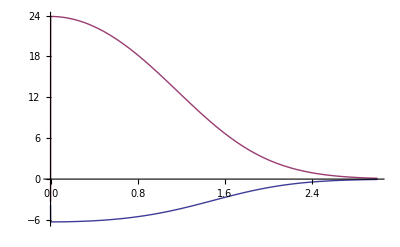

```mathematica
Plot[{Re[V[1.85,r]],Im[V[1.85,r]]},{r,0,3}]
```

```mathematica
χ0[k_,b_]=-2*m/(k*(ℏc)^2)*NIntegrate[V[Sqrt[b^2+z^2]],{z,0,15}];
T0[k_,b_]:=Exp[I*χ0[k,b]]-1
Eif0[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T0[k,b],{b,0,15}]
```

```mathematica
eik0dσdΩ[k_,points_:10]:=Table[{N[θ/points],Abs[Eif0[k,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
En[k_]:=(k*ℏc)^2/(2*m)
U[r_]:=V[r]/V[.01]
ϵ[k_]:=V[.01]/(2*En[k])
```

```mathematica
τ1[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+b*D[#,b])&[U[Sqrt[z^2+b^2]]^2]],{z,0,15}];
```

```mathematica
T1[k_,b_]:=Exp[I(χ0[k,b]+τ1[k,b])]-1
Eif1[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T1[k,b],{b,0,15}]
```

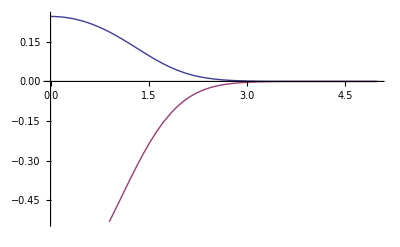

```mathematica
Plot[{Re[χ0[1.85,b]],Im[χ0[1.85,b]]},{b,0,5}]
```

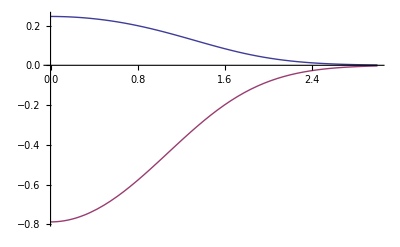

```mathematica
Plot[{Re[-I*Log[σ/(4*Pi*β)(1-I*ep)*E^(-b^2/(2*β))+1]],Im[-I*Log[σ/(4*Pi*β)(1-I*ep)*E^(-b^2/(2*β))+1]]},{b,0,3}]
```

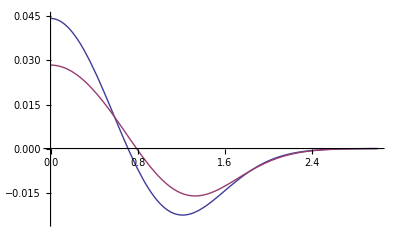

```mathematica
Plot[{Re[τ1[1.85,b]],Im[τ1[1.85,b]]},{b,0,3},PlotRange->{-0.025,0.045}]
```

```mathematica
τ1[1.85,0]
```

0.0443315+0.028428 ⅈ

```mathematica
β0={0.025525,0.080309,0.14877,0.25267,0.46807,1.4727};
α0={0.0014379,0.013487,0.040847,0.092103,0.18785,0.38315,0.86392,2.6165,24.542};
C0={{9.6395*10^-6,6.5959*10^-4,-2.2601*10^-3,2.5861*10^-3,-1.1006*10^-3,1.7251*10^-4},{-3.8282*10^-3,1.8785*10^-2,1.5663*10^-2,-3.8442*10^-2,1.6119*10^-2,-1.2993*10^-3},{-1.0250*10^-2,-7.0482*10^-2,7.1581*10^-2,1.8595*10^-1,-8.3598*10^-2,2.5213*10^-4},{5.3943*10^-3,4.7633*10^-2,-5.3326*10^-1,5.0441*10^-1,1.5834*10^-1,1.3848*10^-2},{-1.3885*10^-2,-1.0979*10^-1,7.5942*10^-1,-1.4875,6.4663*10^-1,-3.0116*10^-2},{7.9833*10^-4,5.6057*10^-2,-6.1065*10^-1,1.0816,-5.6129*10^-1,5.1744*10^-2},{-8.8342*10^-3,-5.9414*10^-2,2.5320*10^-1,-5.2121*10^-1,3.6938*10^-1,3.9780*10^-2},{3.3161*10^-2,1.2733*10^-1,4.3251*10^-2,3.0788*10^-1,-6.0045*10^-1,-7.5965*10^-2},{-2.5412*10^-3,-1.1125*10^-2,6.5278*10^-3,-4.1054*10^-2,5.9130*10^-2,7.9525*10^-4}};
```

```mathematica
β1={3.8566*10^-2,1.2955*10^-1,2.9017*10^-1,9.7471*10^-1};
α1={4.7124*10^-3,4.8770*10^-2,1.8785*10^-1,7.2358*10^-1,7.4885};
C1={{6.1464*10^-6,4.6065*10^-6,-2.2756*10^-5,4.7736*10^-6},{3.6418*10^-5,2.2433*10^-3,3.4320*10^-3,-6.8707*10^-4},{1.9483*10^-5,-2.9031*10^-3,2.0603*10^-2,1.2715*10^-2},{-3.0275*10^-5,1.4127*10^-3,-2.3423*10^-2,-2.8375*10^-3},{-1.2199*10^-5,-1.6321*10^-3,-2.9310*10^-3,4.6651*10^-3}};
```

```mathematica
Sqrt[.071*2*.938]
```

0.36496

```mathematica
nptab=Import["/phys/users/mbuuck/Desktop/npsig.csv"]
pntab=Import["/phys/users/mbuuck/Desktop/pnsig.csv"]
pnepsilontab=Import["/phys/users/mbuuck/Desktop/pnepsilon.csv"]
```

{{0.00385,20360.},{0.03043,6202.},{0.03873,4700.},{0.04347,4228.},{0.04502,4060.},{0.04973,3675.},{0.05,3609.5},{0.0502,3630.},{0.051,3542.9},{0.052,3472.1},{0.053,3398.6},{0.05311,3447.},{0.054,3326.5},{0.05448,3330.},{0.055,3266.6},{0.056,3206.6},{0.057,3138.6},{0.058,3079.6},{0.059,3015.5},{0.0597,3004.},{0.06,2963.6},{0.061,2907.2},{0.062,2851.3},{0.063,2792.6},{0.064,2754.},{0.065,2705.5},{0.06571,2677.},{0.066,2651.5},{0.067,2607.4},{0.068,2558.2},{0.069,2507.},{0.06907,2536.},{0.06913,2525.},{0.07,2464.},{0.071,2433.5},{0.07121,2417.},{0.072,2380.4},{0.073,2341.5},{0.074,2295.9},{0.075,2258.5},{0.076,2225.},{0.07633,2274.},{0.077,2185.9},{0.07767,2206.},{0.078,2151.},{0.079,2123.9},{0.08,2091.},{0.081,2049.9},{0.08112,2067.},{0.082,2017.},{0.083,1988.9},{0.084,1945.4},{0.085,1920.},{0.0857,1948.},{0.086,1893.5},{0.087,1864.},{0.08787,1730.},{0.088,1845.},{0.089,1812.5},{0.08999,1829.},{0.09,1782.},{0.091,1744.4},{0.092,1727.},{0.093,1701.8},{0.094,1675.8},{0.0941,1679.},{0.09459,1690.},{0.095,1653.5},{0.096,1626.2},{0.097,1601.1},{0.09798,1620.},{0.098,1577.3},{0.099,1577.2},{0.1,1533.1},{0.101,1516.1},{0.10176,1517.},{0.102,1489.4},{0.103,1468.5},{0.104,1447.1},{0.105,1427.2},{0.10541,1454.},{0.106,1402.},{0.107,1388.6},{0.108,1367.7},{0.109,1346.4},{0.11,1329.8},{0.111,1308.6},{0.112,1290.3},{0.11245,1327.},{0.113,1274.1},{0.114,1255.6},{0.115,1238.1},{0.11564,1263.},{0.116,1218.},{0.1163,1240.},{0.117,1203.},{0.118,1188.},{0.119,1170.8},{0.12,1155.3},{0.121,1138.8},{0.122,1127.5},{0.12287,1134.},{0.123,1109.7},{0.124,1099.6},{0.125,1083.1},{0.126,1066.9},{0.127,1052.4},{0.128,1038.},{0.12867,1040.},{0.129,1024.3},{0.13,1013.8},{0.13047,1026.},{0.131,1002.6},{0.132,990.21},{0.134,965.19},{0.135,948.24},{0.136,938.6},{0.137,927.03},{0.13745,945.},{0.138,913.8},{0.139,902.6},{0.14,892.87},{0.14032,940.},{0.141,883.72},{0.142,874.51},{0.143,863.56},{0.144,853.04},{0.14419,871.},{0.145,844.37},{0.14505,880.},{0.146,832.26},{0.147,820.73},{0.148,811.12},{0.149,800.64},{0.15,793.},{0.15064,809.},{0.151,782.71},{0.152,774.13},{0.153,766.97},{0.15377,690.},{0.154,755.83},{0.155,745.52},{0.156,736.17},{0.15681,749.},{0.157,727.95},{0.15762,760.},{0.158,719.31},{0.159,712.13},{0.15985,694.},{0.16,703.26},{0.161,695.43},{0.162,686.08},{0.1628,690.},{0.1628,686.},{0.16292,720.},{0.163,678.44},{0.16339,690.},{0.16339,689.},{0.164,670.72},{0.165,662.77},{0.166,656.77},{0.167,650.32},{0.168,642.11},{0.16853,640.},{0.16856,662.},{0.169,635.37},{0.17,628.45},{0.171,618.76},{0.17137,648.},{0.172,615.16},{0.173,537.},{0.173,608.56},{0.174,601.03},{0.17413,582.},{0.175,594.86},{0.175,634.},{0.176,588.04},{0.17686,609.},{0.177,581.75},{0.177,580.},{0.178,576.73},{0.178,597.},{0.179,569.24},{0.17954,612.},{0.18,563.15},{0.18,561.},{0.181,558.7},{0.182,544.},{0.182,552.03},{0.18218,587.},{0.183,547.79},{0.18375,560.},{0.184,540.36},{0.184,533.},{0.18479,539.},{0.185,534.22},{0.186,517.},{0.186,526.15},{0.187,522.88},{0.188,523.},{0.188,518.45},{0.189,513.93},{0.19,498.},{0.19,507.95},{0.191,502.9},{0.192,497.93},{0.19274,493.3},{0.19281,498.},{0.193,492.44},{0.193,522.},{0.19324,494.2},{0.19324,495.},{0.194,487.73},{0.19455,504.},{0.195,479.},{0.195,484.43},{0.19519,479.},{0.196,478.55},{0.197,479.},{0.197,476.},{0.19782,470.},{0.198,470.06},{0.19884,467.},{0.199,449.},{0.199,464.2},{0.2,459.5},{0.201,455.9},{0.202,447.},{0.202,450.55},{0.20243,448.},{0.203,446.96},{0.204,420.},{0.204,439.34},{0.20418,432.},{0.205,436.4},{0.206,430.35},{0.207,408.},{0.207,426.59},{0.208,425.55},{0.209,433.},{0.209,421.4},{0.20923,411.},{0.21,418.45},{0.211,397.7},{0.211,414.63},{0.212,408.09},{0.213,403.45},{0.2135,397.2},{0.214,401.2},{0.214,393.},{0.215,395.1},{0.216,393.4},{0.21609,388.},{0.21654,385.5},{0.217,393.5},{0.217,389.59},{0.218,384.68},{0.219,382.49},{0.2195,388.},{0.22,362.9},{0.22,379.59},{0.221,373.55},{0.222,377.6},{0.222,369.6},{0.22263,367.},{0.223,369.64},{0.22395,329.},{0.224,365.89},{0.225,345.7},{0.225,363.53},{0.226,358.2},{0.227,354.29},{0.228,335.4},{0.228,351.4},{0.229,348.},{0.22905,347.},{0.23,345.91},{0.23087,337.6},{0.231,321.5},{0.231,341.61},{0.232,333.5},{0.23234,340.},{0.233,334.3},{0.234,312.2},{0.234,330.7},{0.235,328.9},{0.23524,331.},{0.236,329.4},{0.23626,315.8},{0.237,323.45},{0.238,309.1},{0.238,320.45},{0.239,316.1},{0.24,311.24},{0.241,281.7},{0.241,313.},{0.24118,287.},{0.242,306.52},{0.243,311.6},{0.244,286.4},{0.244,304.1},{0.245,297.2},{0.246,302.5},{0.247,295.94},{0.248,288.7},{0.248,294.5},{0.249,290.19},{0.25,289.3},{0.251,276.},{0.251,287.},{0.252,285.5},{0.255,260.1},{0.259,245.8},{0.263,220.},{0.26383,247.5},{0.267,226.8},{0.26991,223.},{0.272,223.5},{0.27351,227.23},{0.27551,223.7},{0.276,219.1},{0.27707,170.},{0.281,204.6},{0.28406,203.},{0.28406,203.25},{0.286,196.},{0.291,189.1},{0.29426,190.31},{0.296,187.3},{0.29818,185.4},{0.30088,196.},{0.301,170.3},{0.30414,173.38},{0.307,166.8},{0.30757,167.8},{0.312,152.},{0.31375,163.1},{0.318,152.},{0.32309,150.19},{0.32423,151.5},{0.325,144.8},{0.331,141.5},{0.3322,142.64},{0.338,135.8},{0.33919,133.3},{0.3411,134.25},{0.344,124.3},{0.34979,125.21},{0.34979,126.},{0.35122,116.8},{0.3583,118.86},{0.35858,114.9},{0.366,109.6},{0.36664,112.51},{0.37481,107.77},{0.375,100.1},{0.38283,102.88},{0.384,100.3},{0.39071,97.32},{0.393,94.7},{0.39846,93.544},{0.403,85.3},{0.40608,90.375},{0.413,82.1},{0.41359,86.193},{0.41606,84.5},{0.417,85.7},{0.42098,83.},{0.42098,76.},{0.42098,82.783},{0.424,77.7},{0.42826,80.316},{0.42923,77.},{0.43306,73.9},{0.43306,73.},{0.435,72.1},{0.43545,77.676},{0.43782,74.},{0.43829,76.},{0.44,76.6},{0.44253,75.247},{0.447,71.5},{0.44744,80.},{0.44953,73.636},{0.45644,70.841},{0.459,69.4},{0.46054,59.},{0.46326,68.958},{0.468,68.3},{0.47001,67.234},{0.471,68.3},{0.47667,65.355},{0.48327,63.2},{0.48327,61.5},{0.489,62.8},{0.48979,61.82},{0.49625,60.388},{0.50264,56.9},{0.50264,59.424},{0.50897,58.41},{0.51,58.},{0.51524,57.021},{0.52145,56.165},{0.5276,54.876},{0.53168,48.5},{0.533,54.5},{0.5337,53.991},{0.53975,53.367},{0.54575,51.768},{0.5517,51.017},{0.553,51.7},{0.5576,50.768},{0.5576,46.4},{0.56346,50.425},{0.56346,50.5},{0.56927,49.544},{0.57119,51.2},{0.57503,48.831},{0.58076,47.936},{0.58645,47.638},{0.58833,49.2},{0.59209,46.318},{0.5977,45.961},{0.60327,45.272},{0.60881,44.},{0.60881,45.05},{0.61431,44.501},{0.61977,43.976},{0.6252,43.446},{0.6306,43.254},{0.63597,42.87},{0.64131,42.022},{0.64485,41.918},{0.64501,42.7},{0.66236,41.04},{0.66582,42.46},{0.67957,41.3},{0.67957,41.},{0.67957,39.966},{0.69649,38.963},{0.71316,38.085},{0.725,42.8},{0.72958,37.144},{0.74577,36.819},{0.75857,38.13},{0.76175,38.},{0.76175,33.},{0.76175,36.355},{0.775,38.63},{0.77753,35.582},{0.79313,35.106},{0.80854,34.563},{0.82379,34.56},{0.825,37.32},{0.83738,36.14},{0.83888,34.1},{0.85382,33.938},{0.86862,33.487},{0.875,33.97},{0.88329,33.749},{0.89783,33.163},{0.9108,35.05},{0.91224,32.68},{0.925,34.09},{0.92654,32.685},{0.94073,32.771},{0.95481,32.417},{0.96879,33.7},{0.96879,32.408},{0.975,33.9},{0.97851,34.53},{0.98267,32.548},{0.99646,32.914},{1.01016,32.41},{1.02377,32.634},{1.024,33.57},{1.03731,32.714},{1.05076,32.952},{1.06414,32.813},{1.075,34.16},{1.07744,33.154},{1.08407,35.15},{1.09067,33.308},{1.10384,33.139},{1.11694,33.231},{1.125,34.94},{1.12998,33.055},{1.14295,33.623},{1.15587,34.021},{1.16873,33.732},{1.175,35.47},{1.18153,34.662},{1.19428,34.354},{1.20698,34.609},{1.21962,35.318},{1.225,36.04},{1.23222,34.665},{1.24478,35.347},{1.25728,35.875},{1.25728,35.2},{1.26974,35.745},{1.275,36.85},{1.28216,36.117},{1.29454,36.486},{1.30688,36.953},{1.31917,37.415},{1.325,37.6},{1.33143,37.19},{1.34365,37.357},{1.35584,37.848},{1.36798,38.197},{1.375,37.85},{1.3801,38.493},{1.39218,38.263},{1.40423,38.241},{1.41624,38.656},{1.425,37.98},{1.42823,38.318},{1.5,37.82},{1.6,38.12},{1.7,38.21},{1.8,38.85},{1.9,39.35},{2.022,39.99},{2.14261,42.4},{2.193,40.5},{2.391,40.67},{2.627,40.75},{2.944,40.76},{3.,43.},{3.277,40.83},{3.4126,38.1},{4.,43.1},{4.3,40.4},{4.7476,43.4},{5.7,42.5},{5.86478,33.6},{6.3706,41.2},{6.37066,41.2},{6.5,38.7},{7.7831,39.3},{8.,39.7},{8.2468,41.2},{9.1919,40.8},{10.,39.5},{11.,39.4},{12.,39.3},{13.,39.},{14.,38.7},{14.6,37.1},{16.,39.1},{17.,38.5},{17.8,37.5},{18.,38.7},{21.,38.5},{21.6,37.7},{26.2832,38.94},{26.5,39.3},{27.,38.9},{34.,38.2},{34.,38.2},{36.5879,38.85},{52.6916,38.2},{80.,38.98},{80.,38.98},{131.,39.17},{131.,39.14},{133.,39.21},{175.,39.21},{180.,39.52},{180.,39.62},{215.,39.79},{215.,39.79},{240.,39.66},{240.,39.66},{273.,40.32},{273.,40.32},{310.,39.6}}

{{0.5,42.9},{0.59,40.9},{0.66,37},{0.83,32.5},{0.94,32},{1.08,31.8},{1.11,35.72},{1.19,30.7},{1.24,31.1},{1.28,31.7},{1.29,38.64},{1.41,39.44},{1.59,39.2},{1.61,39.77},{1.66,40.09},{1.78,40.56},{1.86,41.22},{1.94,41.53},{1.95,41.48},{2.08,41.91},{2.21,42.17},{2.28,42.5},{2.45,42.68},{2.59,42.89},{2.68,42.96},{2.7,42.93},{2.82,43.02},{2.86,43.04},{2.96,43.11},{2.99,43.12},{3.05,42.98},{3.11,43.23},{3.14,43.12},{3.27,37.1},{3.28,42.81},{3.3,42.99},{3.44,42.58},{3.55,42.52},{3.91,42.53},{4.04,42.5},{4.26,42.28},{4.51,36.8},{4.55,42.26},{4.97,42.07},{5.22,42.02},{5.53,42.03},{5.82,41.82},{5.83,37},{6,42.6},{7.75,37.6},{7.84,41.33},{8,41.8},{10,41.5},{12,40.4},{14,40.2},{15,39.68},{16,40.2},{18,39.2},{19.8,38.7},{20,39.06},{20,38.7},{22,38.2},{23,38.52},{25,38.79},{30,38.84},{35,39.15},{35,38.58},{40,38.65},{45,38.28},{50,38.96},{50,38.86},{50,38.5},{55,38.35},{60,38.51},{70,38.95},{100,38.96},{100,38.85},{120,39.02},{150,39.07},{150,39.02},{170,39.18},{200,39.27},{200,39.18},{240,39.5},{280,39.53},{310,39.75},{340,39.72},{370,40.01}}

{{0.6,-0.48},{1.69,-0.5},{11.2,-0.21},{15.9,-0.38},{20.5,-0.35},{26.5,-0.35},{34.8,-0.25},{48.9,-0.14},{48.991,-0.081},{57.2,-0.2},{64.8,0.13},{70.2,-0.14},{81.9946,-0.127},{181.998,-0.065},{280.998,-0.084},{378.999,-0.045},{396.999,0.021}}

```mathematica
pnepsilon=Interpolation[pnepsilontab]
```

InterpolatingFunction[{{0.6,396.999}},<>]

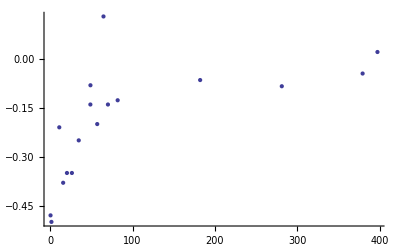

```mathematica
ListPlot[pnepsilontab]
```

```mathematica
pnepsilon[0.36496027181050816]
```

InterpolatingFunction::dmval: Input value {0.36496027181050816`} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.472201

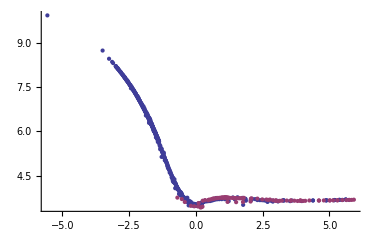

```mathematica
ListPlot[{Log[nptab],Log[pntab]}]
```